```mathematica
xMin=-6;xMax=6;
n=101;                  
x=Subdivide[xMin,xMax,n-1];
dx=x[[2]]-x[[1]];


V=DiagonalMatrix[(x^2)/2.];
V1=DiagonalMatrix[(x^4)]/40.;

main=ConstantArray[-2.,n];
off=ConstantArray[1.,n-1];
D2=SparseArray[{Band[{1,1}]->main,Band[{1,2}]->off,Band[{2,1}]->off},{n,n}]/dx^2;

T=-(1/2.) D2;

H=T+V+V1;


{vals,vecs}=Eigensystem[H];
```

```mathematica
vals[[100]]-vals[[101]]
vals[[99]]-vals[[100]]
```

1.06404

1.12014

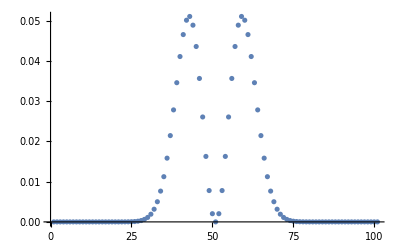

```mathematica
ListPlot[Abs[vecs[[100]]]^2]
```

```mathematica
A=0.01;
xmatr=DiagonalMatrix[x];
w=vals[[100]]-vals[[101]];
h[t_]:=H+A xmatr Sin[w t];
c0=vecs[[101]];
c={};
AppendTo[c,c0];
tmax=1000;
dt=0.1;
Nt=tmax/dt;
Do[
t=(i-1)dt;
U=MatrixExp[-I h[t] dt];
c0=U.c0;
AppendTo[c,c0];
,{i,1,Nt}]
```

```mathematica
ListAnimate[Table[ListPlot[Abs[c[[IntegerPart[i/dt]+1]]]^2],{i,0,10-dt}]]
```

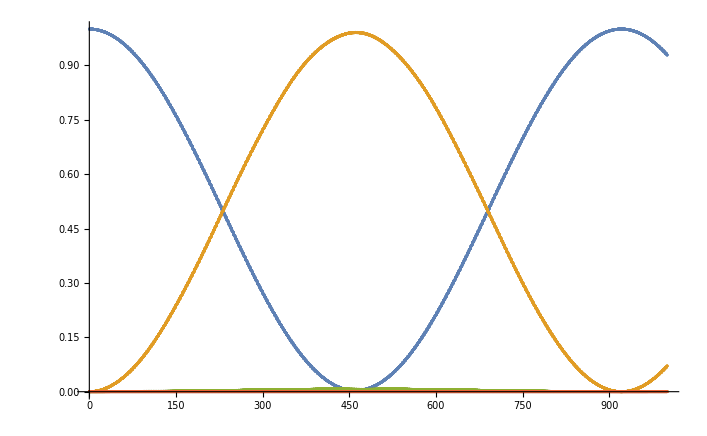

```mathematica
p0[i_]:=Abs[Conjugate[c[[IntegerPart[i/dt]+1]]].vecs[[101]]]^2;
p1[i_]:=Abs[Conjugate[c[[IntegerPart[i/dt]+1]]].vecs[[100]]]^2;
p2[i_]:=Abs[Conjugate[c[[IntegerPart[i/dt]+1]]].vecs[[99]]]^2;
p3[i_]:=Abs[Conjugate[c[[IntegerPart[i/dt]+1]]].vecs[[98]]]^2;
ListPlot[{Table[{i,p0[i]},{i,0,tmax,dt}],Table[{i,p1[i]},{i,0,tmax,dt}],Table[{i,p2[i]},{i,0,tmax,dt}],Table[{i,p3[i]},{i,0,tmax,dt}]},PlotRange->All]
```

```mathematica
Nt
Abs[Conjugate[c[[IntegerPart[Nt/dt]+1]]].vecs[[101]]]^2
```

100.

Part::partw: Part 1001 of {{3.44549×10^-9,8.62755×10^-9,1.79809×10^-8,3.56661×10^-8,6.91752×10^-8,1.32041×10^-7,«40»,0.231945,0.243967,0.252934,0.258472,«51»},«50»} does not exist.